## Timeline of the Korean government’s public health measures in response to COVID-19 epidemic

## Data compilation

```mathematica
data={<|
"The Korean government raises the alert level(Blue)"->{2020,01,03},
"Genetic sequence of the 2019-nCoV revealed"->{2020,01,12},"The first confirmed case reported"->{2020,01,20},
"The Korean government raises the alert level(Yellow)"->{2020,01,20},
"Immigration policy decision to question all travelers from Hubei, China"->{2020,01,20},"Immigration policy decision to isolate/quarantine infected patients traveling from Hubei, China"->{2020,01,20},
"The Korean government's first high-level Emergency Committee Meeting"->{2020, 01,22},"Travel ban imposed on Hubei Province in China"->{2020,01,27},
"KCDC convenes an emergency meeting with representatives from private pharmaceutical companies to develop diagnostic test kits"->{2020,01,27}, 
"Korean government raises the infectious disease alert level(Orange)"->{2020,01,28},
"The KCDC and the National Health Insurance Service introduce 1339 call center to receive consulation calls from the public"->{2020,01,29},
"WHO declares the coronavirus, global health emergency"->{2020,01,30},
"The first secondary confirmed case reported"->{2020,01,31},
"The first fast-tract approval('Emergency Use Authorization')of selected test kits and national distribution begins(daily testing capacity of 3000)"->{2020,01,31},
"Banning entry of all foreign nationals who travelled to Hubei Province in China"->{2020,02,4},
"COVID-19 test kits became available in private hospitals"->{2020,02,07},
"The first big cluster of infection detected(Taegu)"->{2020,02,19},
"The number of confirmed cases reach 100 and the first death case reported"->{2020,02,20},
"The first'Special Management Region'(Taegu) declared; The KCDC requests voluntary mask-wearing and 14 days of self-quarantine in Taegu area"->{2020,02,21},
"The first 'Drive-through' testing site introduced in Chilgok hospital"->{2020,02,23},
"The Korean government raises the alert level (Red, the highest level) and delays the school opening date"->{2020,02,25},
"Goyang city goverment begins to operate Drive-through testing station"->{2020,02,26},
"The Ministry of Economy and Finance announces rent subsidy for small and medium sized firms for 6 months"->{2020,02,28},
"The KCDC advises to practice 'social distancing' and face-mask wearing"->{2020,02,29},
"The KCDC and the Infectious Disease Management introduces a patient classification system and establishes residential treatment centers for isolating/quarantining all incoming intenational travelers"->{2020,03,01},
"The government announces its policy to buy 80% of domestically produced specialty masks to maintain stable supply chain"->{2020,03,05},
"The government introduces GPS-based 'self health check' mobile applications to enforce quarantine measures"->{2020,03,07},
"Special immigration policy to question and quarantine ('entry screening') for incoming travellers from China expanded to include Japan"->{2020,03,09},
"Another big cluster of infection detected (a Call center in Seoul)"->{2020,03,10},
"The Ministery of Education postpones the starting date of new school year until March 23, 2020"->{2020,03,10},
"WHO declares COVID-19 pandemic"->{2020,03,11},
"Entry screening for incoming travellers from China expanded to include Italy and Iran"->{2020,03,11},
"Introducing a case classification system (confirmed case, suspect case, patients under investigation) and issuing a new guideline for suspect and symptomatic individuals "->{2020,03,15},
"Establishing patient management system (classifying patients based upon severity, securing hospital beds and intensive care units, providing protective gear and equipment and managing medicinal supplies,etc)"->{2020,03,15},
"Entry screening expanded to include all Europe"->{2020,03,15},
"Establishing technology-based contact tracing and automatic alert system"->{2020,03,15},
"Expansion of daily testing capacity (18000)"->{2020,03,16},
"The government declares 'Taegu' area as speical disaster zones due to high numbers of confirmed cases"->{2020,03,17},
"The Ministery of Education further postpones the starting date of new school year until April,06 2020"->{2020,03,17},
"Entry screening expanded to all incoming international travellers"->{2020, 03,19},
"Mandatory diagnostic testing introduced in entry screening for all incoming international travelers from China, Europe, and the US"->{2020,03,25},
"'Walk-through' testing station is set up at Incheon international airport"->{2020,03,26},
"'Enhanced social distancing' measure is extended to April 19"->{2020,04,04},
"KCDC releases the data for diagnostic testing capacity (Average 15,000 (maximum 20,000) daily testing by total 118 institutions)"->{2020,04,07},
"Seoul municipal government issues a business suspension order for clubs and bars"->{2020,04,08},
"Schools begin the academic year online"->{2020,04,09},
"The Ministry of Economy and Finance introduces a second supplemental budget of 7.6 trillion KRW to provide 14.87 million households with COVID-19 Relief Funds"->{2020,04, 16},
"The KCDC National Institute of Health announces a plan to conduct domestic clinical trials for COVID-19 vaccine candidate"->{2020,04,16},
"An intergovernmental working level task force on COVID-19 response, comprising both private and public sectors, convenes for its first meeting"->{2020,04,17},
"The government relaxes the enhanced physical distancing measure until May 5"->{2020,04,20},
"The Ministry of Economy and Finance increases 'COVID-19 relief funds' to 135 trillion KRW, including 40 trillion KRW of financial support for strategic industries"->{2020, 04,22},
"The National Assembly approves a 12.2 trillion KRW supplementary budget to fund 'COVID-19 Disaster Relief' financial assistance"->{2020,04,30},
"The government partially reopens state-run museums, art galleries and libraries in compliance with social distancing guidelines"->{2020, 05,01},
"The government begins to pay out emergency disaster relief funds to all households"->{2020,05,04},
"The Ministery of Education announces a plan to reopen schools on May 20"->{2020, 05,04}, "The KCDC ends the strict social distancing campaign and replaces it with a 'distancing in daily life' scheme"->{2020,05,06},
"The Ministry of Economy and Finance begins to pay emergency unemployment insurance program"->{2020,05,07},
"The government issues an advisory to suspend business operation of all clubs and bars for a month"->{2020,05,08},
"Seoul, Incheon, and Gyeonggi Province issue an administrative order to prohibit social gatherings for two weeks"->{2020,05,10},
"Seoul municipal government requires all subway passengers to wear face-masks"->{2020,05,11},
"The government requires all passengers to wear face-mask in public transportation"->{2020,05,25},
"The government to provide 40 trillion KRW in financial assistance to strategic industries (aviation, ship-building, machinary and engineering, etc)"->{2020,05,28},
"The government suspends operations of all state-run museums, galleries, and theaters for two weeks"->{2020,05,29},
"The government lifts 'designated day-only' rule to allow citizens to buy 'public masks' any day of the week"->{2020,06,01},
"The government announces a plan to invest 100 billion KRW to support R&D in developing treatments and vaccine" ->{2020,06,03},
"QR code-based registration of visitors at bars, clubs and entertainment facilities and private educational institutes becomes mandatory across the country after a successful testing in mid-May"->{2020,06,10},
"The KCDC reimpose a level three social distancing measure in response to the confirmed case rebounding to over 60"->{2020,06,28},
"The government ends mask-rationing system after four months"->{2020,07,12},
"The government lifts restrictions on museums, galleries and libraries in Seoul Metropolitan area"->{2020,07,19},
"Daily confirmed cases fall back to below 30 for the first time since the first wave began in March" ->{2020,07,27},
"Bank of Korea extends special loan scheme for commercial banks, brokerage firms and insurance companies by three months"->{2020,07,30},
"The legal status of the Korea Centers for Disease Control and Prevention (KCDC) under the Ministry of Health and Welfare is elevated to an independent administrative agency, the Korea Disease Control and Prevention Agency(KDCA)"->{2020,08,04},
"New daily confirmed cases fall back to 20 with local infection cases fall below to a single digit"->{2020,08,07},
"The Food and Drug Safety Agency approves clinical trials for another local COVID-19 drug candidate" ->{2020,08,07},
"New daily confirmed cases jump to an over 4-month high of 85"->{2020,08,14},
"Seoul municipal government places tougher restrictions on gatherings at around 7500 religious facilities (including churches and Buddhist temples"->{2020,08,14},
"New daily confirmed cases reach 5-month high of 166 as a church-link political demonstration spread the virus"->{2020,08,15},
"The government raises the three-tier social distancing scheme in Seoul and Gyeonggi Province from level 1 to level 2"->{2020,08,15},
"All schools in Seoul Metropolitan area are closed and shift online until Sept. 11"->{2020,08,25},
"The Food and Drug Safety Agency approves clinical trials for another local COVID-19 drug candidate"->{2020,08,26},
"Seoul municipal government restricts operating hours of restaurants and bakers in Metropolitan area and extends 542.3 billion KRW in emergency disaster relief fund to 1.6 million households"->{2020,08,26},
"The government proposes a second supplementary budget (about 7 trillion KRW) with a plan to provide another round of emergency disaster relief financial assistance to selected needy households and self-employed"->{2020,09,06},
"The Food and Drug Safety Agency approves a test kit that detects and discerns the novel coronavirus and seasonal flu infection"->{2020,09,08},
"The government announces a decision to slightly ease social distancing measure from level 2.5 to level 2"->{2020,09,13},
"The Ministry of Education announces schools in Seoul and its adjacent cities resume in-person classes on Sept. 21, 2020 as new daily confirmed cases fall below 200 for more than 10 days"->{2020,09,15},
"The Food and Drug Safety Agency announces approval of advanced clinical trials for Celltrion Inc.'s CT-P59 treatment"->{2020,09,17},
"Daily confirmed cases fall below 100 for the first time more than a month with total 72 local infection cases"->{2020,09,20},
"Childcare centers and schools in Seoul and its adjacent areas resume limited in-person classes"->{2020,09,21},
"The government introduces a new set of detailed social distancing guidelines ranging from level 1 to level 3 (to be effective on Nov. 01)"->{2020,09,25},
"Major state-run cultural facilities reopen under strict distancing and sanitary measures"->{2020,09,28},
"The government announces to impose fine (up to 100,000 KRW) for those who are not wearing face mask in public space (to be effective on Nov. 13)"->{2020,10,04},
"Daily confirmed cases rebound over 100 after more than three-week long double records"->{2020,10,22},
"Mandatry mask wearing in all publicly used facilities becomes effective with 100,000KRW fine for violation"->{2020,11,13},
"Daily confirmed cases rises over 200 for the first time in 73 days"->{2020,11,14},
"Daily confirmed cases rise to 313 with total 245 local infections"->{2020,11,18},
"Seoul municipal government announces a plan to increase the number of contact tracing agents from 30 to 190 amid a sharp rise in new confirmed cases"->{2020,11,18},
"Seoul municipal government raises its social distancing rules to level 2"->{2020, 11,22},
"Daily confirmed cases surpasses 500 for the first time in over eight months with total 553 local infections"->{2020,11,26},
"Daily confirmed cases tops 600, the most in nearly nine months with total 600 local infections"->{2020,12,04},
"Seoul municipal government announces to suspend all business operation of restaurants, shops, and movie theaters and to close public office buildings on 9 pm for two weeks (to be effective on Dec. 07)"->{2020,12,05},
"All schools in Seoul Metropolitan area are ordered to suspend in-person classes"->{2020,12,05},
"The government announces to raise the social distancing level from 2 to 2.5 level in Seoul and its adjacent areas for three weeks(to be effective on Dec. 08)"->{2020,12,06},
"The KDCA announces to use antigen test kits (using saliva), in addition to PCR test kits, in order to make it more convenient to get the test"->{2020,12,08}


|>};
```

## Timeline plot

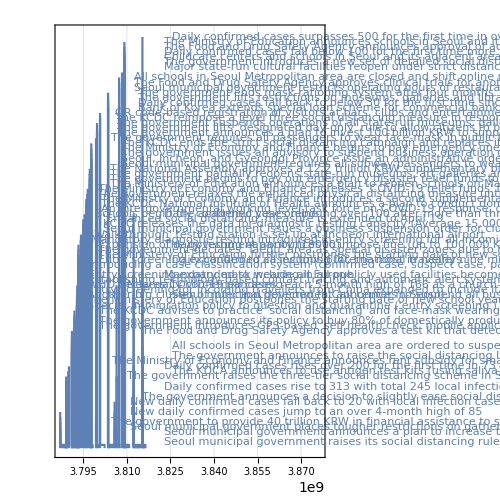

```mathematica
TimelinePlot[data,PlotTheme->"Detailed",PlotLabel->"Timeline of public health measures in response to COVID-19 epidemic in Korea",PlotLegends->Placed[{"Source: The author's compilation of the KDCA's press releases"},Below],PlotRange->Full,Axes->True,Frame->Automatic]
```

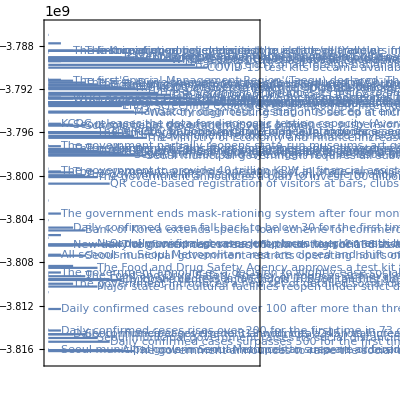

```mathematica
TimelinePlot[data,PlotTheme->"Detailed",PlotLayout->"Vertical",PlotLabel->"Timeline of the Korean government's public health measures in response to COVID-19 epidemic",PlotLegends->Placed[{"Source: The author's compilation of the KDCA's press releases"},Below],PlotRange->Automatic,Axes->True,Frame->Automatic,ImageSize->{Automatic,600},GridLines->{Automatic,None}]
```

## New set of social distancing levels (Nov. 01, 2020)

Levels |  | Level 1 | Level 1.5 | Level 2 | Level 2.5 | Level 3
Purpose |  | Preventive measures | Local transmission |  | Nationwide community transmission | 
When to issue |  | Distancing in Daily Life | Beginning of local circulation | Rapid spread of local transmission & beginning of nationwide transmission | Nationwide community transmission intensifies | Nationwide massive community transmission
Core indicators | Weekly average of daily local transmission cases (n) | (1) Seoul Metropolitan area - below 100
(2)Gangwon and Jeju - below 10
(3) Other regions - below 30 | (1) Seoul Metropolitan area - 100 or more
(2)Gangwon and Jeju - 10 or more
(3) Other regions - 30 or more | If one of the following situations happens:
(1)Case numbers double or more of the criteria for level 1.5
(2)Transmission continues in 2 or more regions
(3) More than 300 new cases nationwide | 400-500 or more new cases per day or a rapid surge in the number of confirmed cases (such as doubling) | 800-1000 or more new cases per day or a rapid surge in the number of confirmed cases (such as doubling)
Supplmenetary indicators | (1) Weekly average of number of confirmed cases aged 60 or above, (2)Hospital bed capacity to treat severe/critical cases, (3) Epidemic investigation capacity, (4) Basic reproduction number, (5) Cluster infection situation, (6) Percentage of cases with transmission chain under investigation, (7) Percentage of cases confirmed while under home quarantine |  |  |  |  |

Source: KDCA Press Release (Nov. 11, 2020) (http://www.kdca.go.kr/board/board.es?mid=a30402000000&bid=0030)

## Reference

Ministry of Economy and Finance, “Tackling COVID-19: Health, Quarantine and Economic Measures of South Korea”, Ministry of Economy and Finance, South Korea

Amy Dighe et al, “Response to COVID - 19 in South Korea and implications for lifting stringent interventions”, BMC Medicine (2020) 13:321 (https://doi.org/10.1186/s12916-020-01791-8)

Chad Terhune, Dan Levine, Hyunjoo Jin, Jane Lanhee Lee, “Special Report: How Korean trounced U.S. in race to test people for coronavirus”, Reuters, March 18, 2020

Emilio Parodi, Stephen Jewkes, Sangmi Cha, Ju-min Park, “Special Report: Italy and South Korea virus outbreaks reveal disparity in deaths and tactics”, Reuters, March 12, 2020

Max Fisher and Choe Sang-Hun, “How South Korea Flattened the Curve”, The New York Times, March 23, 2020

Juhwan Oh, Jong-Koo Lee, Dan Schwarz d, Hannah L. Ratcliffe, Jeffrey F. Markuns,
and Lisa R. Hirschhorn, "National Response to COVID-19 in the Republic of Korea and Lessons Learned for Other Countries”, HEALTH SYSTEMS & REFORM 2020, VOL. 6, NO. 1, e1753464 (https://doi.org/10.1080/23288604.2020.1753464)

Victor Cha and Dana Kim, “A Timeline of South Korea’s Response to COVID-19”, CSIS Newsletter, 2020 March 27